0.28612-0.000305635 x+0.0113034 x^2

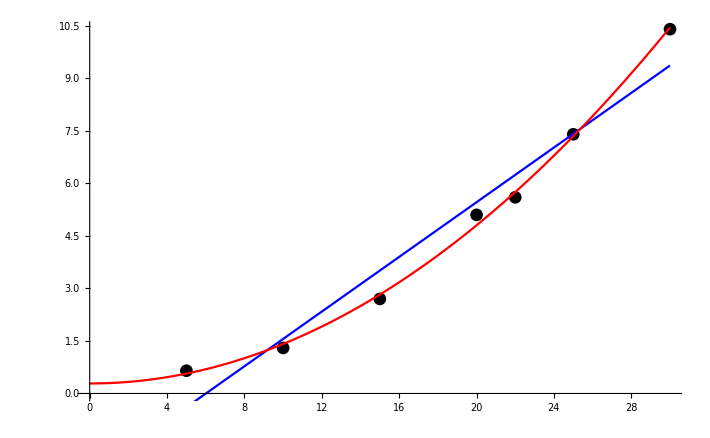

```mathematica
data = {{5,0.65},{10,1.3},{15,2.7},{20,5.1},{22,5.6},{25,7.4},{30,10.4}};

firstDeg = Fit[data,{1,x},x];
secondDeg= Fit[data,{1,x, x^2},x]

Show[
ListPlot[data,PlotStyle-> {Black}],
Plot[Function[firstDeg][x],{x,0,30}, PlotStyle->{Blue}],
Plot[Function[secondDeg][x],{x,0,30}, PlotStyle->{Red}]
]
```

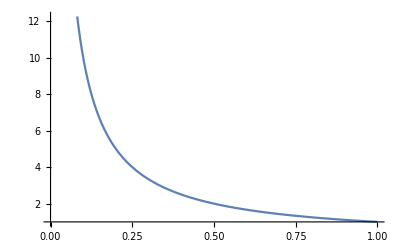

```mathematica
surprise = Function[1/x*1];

Plot[surprise[x],{x,0,1}]
```